β/λa

Set::write: Tag Plus in A2 - D2 is Protected.

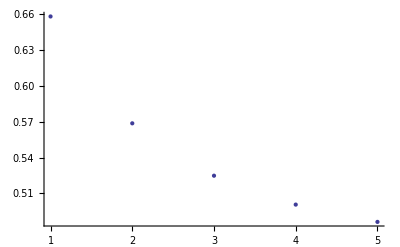

ListPlot::nonopt: Options expected (instead of 0.658117
0.568706
0.524882
0.500709
0.486234) beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[1
2
3
4
5,0.658117
0.568706
0.524882
0.500709
0.486234]

```mathematica
Notations;
L=a/b;
d=κb;
c=κa;
a=λa;
b=λb;
bts1=β/b;
bts2=β/a
A2-D2=Terms in equation (38);
Qf=scaled charge density;




d=Table[i,{i,1, 5, 1}];
L=0.5;
c=d*L;
b=1.02;
a=b*L;
Qf=1.88;
bts1=1.0;
bts2=(bts1/L);
x=c+a;
y=d+b;
x1=-c+a;
y1=-d+b;
x2=c-a;
y2=d-b;
x3=-c-a;
y3=-d-b;
E3d=ExpIntegralE[3,d];
E5d=ExpIntegralE[5,d];
E3c=ExpIntegralE[3,c];
E5c=ExpIntegralE[5,c];
E3Md=ExpIntegralE[3,-d];
E5Md=ExpIntegralE[5,-d];
E3Mc=ExpIntegralE[3,-c];
E5Mc=ExpIntegralE[5,-c];
E3x=ExpIntegralE[3,x];
E5x=ExpIntegralE[5,x];
E3y=ExpIntegralE[3,y];
E5y=ExpIntegralE[5,y];
E3x1=ExpIntegralE[3,x1];
E5x1=ExpIntegralE[5,x1];
E3y1=ExpIntegralE[3,y1];
E5y1=ExpIntegralE[5,y1];
E3x2=ExpIntegralE[3,x2];
E5x2=ExpIntegralE[5,x2];
E3y2=ExpIntegralE[3,y2];
E5y2=ExpIntegralE[5,y2];
E3x3=ExpIntegralE[3,x3];
E5x3=ExpIntegralE[5,x3];
E3y3=ExpIntegralE[3,y3];
E5y3=ExpIntegralE[5,y3];


L11=((1.5*L)/(b*b))-((1.5*L*L)/(b*b));
L12=((0.5*L*L*L)+1.0-(0.5*L*L*L*L*bts2)-(L*bts2)+(1.5*L*L*L*bts2)+(3.0*bts2));
L13=(1.0/(1.0+(2.0*bts2)));
L14=(L11*Cosh[b-a])+(L12*L13*Cosh[b-a]);
L15=((1.5*L)/(b*b))-(1.5*L*L);
L16=(0.5*L*L*L)+1.0 -(0.5* L*L*bts2*a*a)-(a*b*bts2);
L17=(1.5*L*L*L*bts2)+(3.0*bts2);
L18=(L15*((Sinh[b-a])/b))+((L16+L17)*L13*((Sinh[b-a])/b));
L1=L14-L18;

L21=(1.5*L*L*(1.0/(a*b)))+(0.5*L*L*L)+1.0+((3.0*L*bts2)/(b*b));
L22=(1.5*L*L*L*bts2)+(3.0*bts2);
L23=(1.0/(1.0+(2.0*bts2)));
L24=((L21*L23)+(L22*L23))*Cosh[b-a];
L25=((1.5*L*L )+(3.0*L*L*bts2)+(a*b*bts2)+(0.5*a*a*L*L*bts2));
L26=(L25*L23)*((Sinh[b-a])/b);
L27=-((1.5*L*L)*(1/(a*b)))-((4.5*L*bts2)*(1.0/(b*b)));
L28=(1.5*L*bts2)*(1.0/(b*b));
L29=(L27*L23)+(L28*L23);
L2=L24+L26+L29;

L31=1.0+(3.0*bts2)-(L*bts2);
L32=(1.0/(1.0+(2.0*bts2)));
L33=(L31*L32)*Cosh[b-a];
L34=(1.0+(3.0*bts2)-(a*b*bts2));
L35=(L34*L32)*((Sinh[b-a])/b);
L3=L33-L35-L;

L41= 1.0+((3.0*bts2)/(a*b))-bts2;
L42=(1.0/(1.0+(2.0*bts2)));
L43=(L41*L42)*Sinh[b-a];
L44=(1.0/b)+((3.0*bts2)/a)-(bts2/b);
L45=(L44*L42)*Cosh[b-a];
L46=((2.0/3.0)*(b/L))+((1.0/3.0)*a*L);
L47=L46*L42;
L4=L43-L45+L47+(1.0/b);

L51=((1.5*L*L) -(1.5*L));
L52=L51*Cosh[b-a];
L53=( (1.5*L*(1.0/b))-(1.5*L*a));
L54=L53*Sinh[b-a];
L55=(a*b)+(0.5*L*L*a*a);
L5=L52+L54-L55;

Fnot=1.0-(1.0/d)+((( 1.0-c)*(1.0+d))/(( 1.0+c)*d))*Exp[-2.0*(d-c)];
A11=(1.0/6.0)*L*L*L*Exp[d]*E3d;
A12=-(1.0/2.0)*L*L*L*(1.0-(2.0*L2)/(3.0*L1)+(2.0*L3/(L1*b*b)))*Exp[d]*E5d;
A13=-(2.0/3.0)*(1.0/d)+(2.0*L2/(3.0*L1*d))*(1.0+(1.0/d));
A14=(L3/(L1*b*b))*(1.0+(0.5*L*L*L)+(1.0/d)+(1.0/(d*d)));
A1=A11+A12+A13+A14;
A2=0.5*A1*Fnot;


Fm11=c*0.5*Exp[x]*(E3x-L*L*E3y)-(1.5/a)*Exp[x]*(E5x-L*L*L*L*E5y)+(1.5/a)+(c/x);
Fm12=-((1.0/b)*(1.0+(L*L*L/2.0))+c/x)*Exp[x-y];
Fm1=Fm11+Fm12;
Fm21=(-c)*0.5*Exp[x1]*(E3x1-L*L*E3y1)-(1.5/a)*Exp[x1]*(E5x1-L*L*L*L*E5y1)+(1.5/a)-(c/x1);
Fm22=-((1.0/b)*(1.0+(L*L*L/2.0))-c/x1)*Exp[x1-y1];
Fm2=Fm21+Fm22;
Fm31=c*0.5*Exp[x2]*(E3x2-L*L*E3y2)+(1.5/a)*Exp[x2]*(E5x2-L*L*L*L*E5y2)-(1.5/a)+(c/x2);
Fm32=-((-1.0/b)*(1.0+(L*L*L/2.0)) +c/x2)*Exp[x2-y2];
Fm3=Fm31+Fm32;
Fm41=-c*0.5*Exp[x3]*(E3x3-L*L*E3y3)+(1.5/a)*Exp[x3]*(E5x3-L*L*L*L*E5y3)-(1.5/a)-(c/x3);
Fm42=-((-1.0/b)*(1.0+(L*L*L/2.0)) -c/x3)*Exp[x3-y3];
Fm4=Fm41+Fm42;
B11=((L3+L4)/L1)*( (1.0-1.0/c)*Fm1+(1.0+1.0/c)*Fm2);
B12=-((L3-L4)/L1)*( (1.0-1.0/c)*Fm3+(1.0+1.0/c)*Fm4);
B1=B11+B12;
B2=-B1*0.25*L*L*(1.0/(b*b*b))*((1.0+d)/(1.0+c))*Exp[-(d-c)];


F2k=1.5*Exp[c]*(E5c-L*L*L*L*E5d)+L*(1.0+0.5*L*L*L)*Exp[-d+c]-1.5;
F2kM=1.5*Exp[-c]*(E5Mc-L*L*L*L*E5Md)+L*(1.0+0.5*L*L*L)*Exp[d-c]-1.5;
F3k=0.5*L*Exp[-d+c]*(1.0+0.5*L*L*L+3.0/d+3.0/(d*d))-0.75*L*L*L*(1.0+2.0/c+2.0/(c*c));
F3kM=0.5*L*Exp[(d-c)]*(1.0+0.5*L*L*L-3.0/d+3.0/(d*d))-0.75*L*L*L*(1.0-2.0/c+2.0/(c*c));
C11=(1.0-L3/L1)*( (1.0-1.0/c)*F2k+(1.0+1.0/c)*F2kM);
C12=-(L3/L1)*( (1.0-1.0/c)*F3k+(1.0+1.0/c)*F3kM);
C1=C11+C12;
C2=-C1*(1.0/3.0)*(1.0/(b*b))*((1.0+d)/(1.0+c))*Exp[-(d-c)];

Dm11=c*0.5*Exp[x]*(E3x-L*L*E3y)-(1.5/a)*Exp[x]*(E5x-L*L*L*L*E5y)+(1.5/a)+(c/x);
Dm12=-((1.0/b)*(1.0+(L*L*L/2.0))+c/x)*Exp[x-y];
Dm1=Dm11+Dm12;
Dm21=(-c)*0.5*Exp[x1]*(E3x1-L*L*E3y1)-(1.5/a)*Exp[x1]*(E5x1-L*L*L*L*E5y1)+(1.5/a)-(c/x1);
Dm22=-((1.0/b)*(1.0+(L*L*L/2.0))-c/x1)*Exp[x1-y1];
Dm2=Dm21+Dm22;
Dm31=c*0.5*Exp[x2]*(E3x2-L*L*E3y2)+(1.5/a)*Exp[x2]*(E5x2-L*L*L*L*E5y2)-(1.5/a)+(c/x2);
Dm32=-((-1.0/b)*(1.0+(L*L*L/2.0)) +c/x2)*Exp[x2-y2];
Dm3=Dm31+Dm32;
Dm41=-c*0.5*Exp[x3]*(E3x3-L*L*E3y3)+(1.5/a)*Exp[x3]*(E5x3-L*L*L*L*E5y3)-(1.5/a)-(c/x3);
Dm42=-((-1.0/b)*(1.0+(L*L*L/2.0)) -c/x3)*Exp[x3-y3];
Dm4=Dm41+Dm42;
D11=((L/b)-(3.0/(b*b)))*(  ((1.0-(1.0/c))*Dm1)+((1.0+(1.0/c))*Dm2) );
D12=-((L/b)+(3.0/(b*b)))*( (1.0-(1.0/c))*Dm3+(1.0+(1.0/c))*Dm4);
D1=D11+D12;
D2=-D1*(1.0/6.0)*(1.0/(b*b))*(bts2/(1.0+(2.0*bts2)))*(L5/L1)*((1.0+d)/(1.0+c))*Exp[-(d-c)];


ListPlot[Re[Qf*(A2+B2+C2+D2)]]
Data1=Column[Re[Qf*(A2+B2+C2+D2)]];
Data2=Column[d,Qf*Re[A2+B2+C2+D2]];
ListPlot[Data2,Data1]
```

ListPlot::nonopt: Options expected (instead of 0.294635
0.294707
0.294778
0.294848
0.294919
0.29499
0.295061
0.295132
0.295202
0.295273) beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[0.0001
0.0002
0.0003
0.0004
0.0005
0.0006
0.0007
0.0008
0.0009
0.001,0.294635
0.294707
0.294778
0.294848
0.294919
0.29499
0.295061
0.295132
0.295202
0.295273]

gNewLine]", 

 RowBox[{

  RowBox[{"x1", "=", 

   RowBox[{

    RowBox[{"-", "c"}], "+", "a"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"y1", "=", 

   RowBox[{

    RowBox[{"-", "d"}], "+", "b"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"x2", "=", 

   RowBox[{"c", "-", "a"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"y2", "=", 

   RowBox[{"d", "-", "b"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"x3", "=", 

   RowBox[{

    RowBox[{"-", "c"}], "-", "a"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"y3", "=", 

   RowBox[{

    RowBox[{"-", "d"}], "-", "b"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"E3d", "=", 

   RowBox[{"ExpIntegralE", "[", 

    RowBox[{"3", ",", "d"}], "]"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"E5d", "=", 

   RowBox[{"ExpIntegralE", "[", 

    RowBox[{"5", ",", "d"}], "]"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"E3c", "=", 

   RowBox[{"ExpIntegralE", "[", 

    RowBox[{"3", ",", "c"}], "]"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"E5c", "=", 

   RowBox[{"ExpIntegralE", "[", 

    RowBox[{"5", ",", "c"}], "]"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"E3Md", "=", 

   RowBox[{"ExpIntegralE", "[", 

    RowBox[{"3", ",", 

     RowBox[{"-", "d"}]}], "]"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"E5Md", "=", 

   RowBox[{"ExpIntegralE", "[", 

    RowBox[{"5", ",", 

     RowBox[{"-", "d"}]}], "]"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"E3Mc", "=", 

   RowBox[{"ExpIntegralE", "[", 

    RowBox[{"3", ",", 

     RowBox[{"-", "c"}]}], "]"}]}], ";"}], "\[IndentingNewLine]",

ListPlot[2.9453
2.35271
2.05513
1.88831
1.7875
1.72304
1.67993
1.65
1.62855
1.61275
1.60082
1.59163
1.58441
1.57864
1.57397
1.57013
1.56694
1.56426
1.56199
1.56005
1.55837
1.55692
1.55565
1.55454
1.55355
1.55268
1.5519
1.5512
1.55058
1.55001
1.5495
1.54903
1.54861
1.54822
1.54787
1.54754
1.54724
1.54697
1.54671
1.54647
1.54626
1.54605
1.54586
1.54568
1.54552
1.54536
1.54522
1.54508
1.54495
1.54483
1.54472
1.54461
1.54451
1.54441
1.54432
1.54424
1.54416
1.54408
1.54401
1.54394
1.54387
1.54381
1.54375
1.54369
1.54364
1.54358
1.54353
1.54349
1.54344
1.5434
1.54335
1.54331
1.54328
1.54324
1.5432
1.54317
1.54314
1.5431
1.54307
1.54305
1.54302
1.54299
1.54296
1.54294
1.54291
1.54289
1.54287
1.54285
1.54282
1.5428
1.54278
1.54277
1.54275
1.54273
1.54271
1.54269
1.54268
1.54266
1.54265
1.54263]

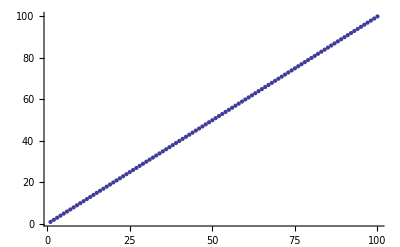

ListPlot::lpn: 4.49009
4.48258
4.67313
4.80926
4.84828
4.80897
4.72046
4.60698
4.48505
4.36472
« 90 » is not a list of numbers or pairs of numbers.

ListPlot::nonopt: Options expected (instead of « 1 ») beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

```mathematica
ListPlot[{{0.0001}, {0.0002}, {0.00030000000000000003}, {0.0004}, {0.0005}, {0.0006000000000000001}, {0.0007000000000000001}, {0.0008}, {0.0009000000000000001}, {0.001}},{{0.29463547713296173}, {0.29470654847828653}, {0.2947775525559729}, {0.29484848946147724}, {0.2949193592900754}, {0.29499016213686247}, {0.29506089809675423}, {0.29513156726448697}, {0.29520216973461966}, {0.2952727056015299}}]
```